```mathematica
i[k_,b_,theta_,a_,n_]:=1/n^2 Sin[k b/2 Sin[theta]]^2/((k b/2)^2Sin[theta]^2) Sin[n k a /2 Sin[theta]]^2/(Sin[k a /2 Sin[theta]]^2)
```

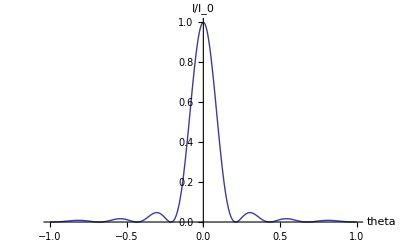

```mathematica
Plot[i[300,0.1,theta,3,1],{theta,-1,1},PlotRange->Full,AxesLabel->{"theta", "I/I_0"}]
```

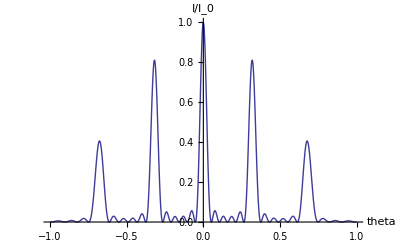

```mathematica
Plot[i[5,1,theta,4,6],{theta,-1,1},PlotRange->Full,AxesLabel->{"theta", "I/I_0"}]
```

```mathematica
lambda=500*^-9
```

1/2000000

```mathematica
a=6000*^-9
```

3/500000

```mathematica
Table[ArcSin[n lambda/a]//N,{n,{0,1,2}}]
```

```mathematica
Table[ArcSin[n lambda/(1000a)]//N,{n,{0,1001,999,1999,2001}}]
```

{0.,0.0835137,0.0833465,0.167364,0.167533}

```mathematica
Solve[.0835137==ArcSin[lambda1/a],lambda1]
```

{{lambda1→5.005×10^-7}}

```mathematica
Solve[.167533==ArcSin[2lambda1/a],lambda1]
```

{{lambda1→5.00251×10^-7}}

```mathematica
0.5/500
```

0.001

```mathematica
0.251/500
```

0.000502